1266

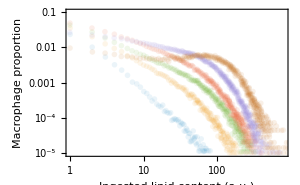

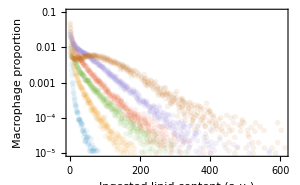

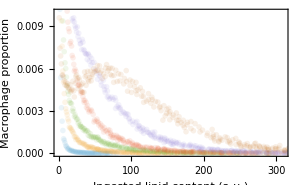

```mathematica
(* resampled experimental data *)
SetDirectory[NotebookDirectory[]];

resamplet0=Join[{{0,1(1-0.05436408687995582)}},Drop[Import["full_initconds.csv","CSV"],1]];
resamplet12=Join[Drop[Import["t12_full.csv"],1]];
resamplet24=Join[Drop[Import["t24_full.csv"],1]];
resamplet36=Join[Drop[Import["t36_full.csv"],1]];
resamplet48=Join[Drop[Import["t48_full.csv"],1]];
resamplet60=Join[Drop[Import["t60_full.csv"],1]];
resamples={resamplet0,resamplet12,resamplet24,resamplet36,resamplet48,resamplet60};

Mdata={{0,1.},{12,0.9762773162434892},{24,0.8759123513425332},{36,0.7481751232867709},{48,0.49635031618480696},{60,0.14233568487147408}};

lipiddata=Drop[Import["avg_LipidContent_data.csv"],1];
lipiddata=Table[{Round[d[[1]]],d[[2]]},{d,lipiddata}];

distributionplot=ListPlot[resamples,PlotRange->{{1,300},{10^(-5),0.01}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (hours)", "Proportion of macrophages"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}];
Mplot=ListPlot[Mdata,PlotMarkers->Automatic,PlotTheme->"Scientific",BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time t (hours)", "Macrophage surviving fraction"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}];
Lplot=ListPlot[lipiddata,PlotMarkers->Automatic,PlotTheme->"Scientific",FrameLabel->{"Time t (hours)", "Mean ingested lipid content (a.u.)"},BaseStyle->{FontFamily->"Cambria Math"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black}];

ndatapoints=Length@resamplet12+Length@resamplet24+Length@resamplet36+Length@resamplet48+Length@resamplet60+(Length@Mdata-1)
{Mplot,Lplot,distributionplot};

opacityval=0.1;
distributionloglogplot=ListLogLogPlot[resamples,PlotRange->{{1,800},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),PlotStyle->{Opacity[opacityval]}]

distributionloglinearplot=ListPlot[resamples,PlotRange->{{1,610},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),ScalingFunctions->{"Linear","Log"},PlotStyle->{Opacity[opacityval]}]

distributionlinearplot=ListPlot[resamples,PlotRange->{{0,310},{0,0.01}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),ScalingFunctions->{"Linear","Linear"},PlotStyle->{Opacity[opacityval]}]

distributionloglogplot48=ListLogLogPlot[Most@resamples,PlotRange->{{1,500},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),PlotStyle->{Opacity[opacityval]}];

distributionloglinearplot48=ListPlot[Most@resamples,PlotRange->{{1,410},{10^(-5),0.1}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300(*,PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"}*),ScalingFunctions->{"Linear","Log"},PlotStyle->{Opacity[opacityval]}];

distributionlinearplot48=ListPlot[Most@resamples,PlotRange->{{0,310},{0,0.02}},Frame->True,PlotTheme->Automatic,PlotMarkers->{●},BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Ingested lipid content (a.u.)", "Macrophage proportion"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Joined->False,ImageSize->300,(*PlotLegends->{"t = 0", "t = 12 h", "t = 24 h", "t = 36 h", "t = 48 h", "t = 60 h"},*)ScalingFunctions->{"Linear","Linear"},PlotStyle->{Opacity[opacityval]}];

negbinom[i_,μ_,cv_]:=Module[{r,p},
r=(μ-1)^2/(cv^2*μ^2-μ+1);
p=(μ-1)/(cv^2*μ^2);
Binomial[i+r-2,i-1]*p^r*(1-p)^(i-1)]

decay[i_?IntegerQ,a_,b_]:=Module[{r,p},
k=(*Sum[N@(j)^(-b),{j,1,1000}];*)Zeta[b];
(1/k)*(i)^(-b)
]

logit[x_]:=Log[x/(1-x)];
invlogit[x_]:=1/(1+Exp[-x]);
```

```mathematica
(* Log-likelihood function *)
ClearAll[loglikelihood];

loglikelihood[{η_?NumericQ,e_?NumericQ,cv_?NumericQ,β0_?NumericQ,β1_?NumericQ,q_?NumericQ,σM_?NumericQ,σm_?NumericQ}]:=
Module[{imax,dx,tmax,n,idx,pmf,βvec,ηvec,fvec,fbar,mInit,eqs,sol,Msol,moutput,Moutput,loglikelihoodm,loglikelihoodM,loglikelihoodL,outcome,λ,Loutput,mRHSfunction,pInit},


imax=1000;
tmax=60;
n=imax+1;
idx=Range[0,imax];

rhsVecfunction[v_?VectorQ,w_?VectorQ,P_,βvec_?VectorQ,n_?IntegerQ]:=Module[{x,h}, (* Here v = (m[0], m[1], ..., m[imax], w = p *)
h=ListConvolve[fvec,ListConvolve[w,v,{1,-1},0],{1,-1},0];
η*(Take[h,n]-P*v)+(βvec.v - βvec)*v
];

pRHSfunction[v_?VectorQ,w_?VectorQ,MM_,βvec_?VectorQ]:=MM*(βvec*v-η*w);

pmf[i_?NumericQ,μ_?NumericQ,sig_?NumericQ]:=Module[{σ2,μLog,σLog,dist},σ2=Log[1+(sig^2/μ^2)];
μLog=Log[μ]-σ2/2;
σLog=Sqrt[σ2];
dist=LogNormalDistribution[μLog,σLog];
CDF[dist,i+1]-CDF[dist,i]];

(*beta_l*)
(*βvec=Developer`ToPackedArray@N@(Table[β0,{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(Table[β0*Exp[β1*t],{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(β0+β1*idx);*)
(*βvec=Developer`ToPackedArray@N@(Table[β1/(1+(β1-β0)/β0*Exp[-t/q]),{i,1,Length[idx]}]);*)
βvec=Developer`ToPackedArray@N@((β0+(β1-β0)*(1-Exp[-idx/q])));


(*eta_l*)
ηvec=Developer`ToPackedArray@N@Table[η,{i,1,n}];
fvec=Developer`ToPackedArray@N@(pmf[#,e,cv*e]&/@(idx+1)); (*g_l*)
mInit=Developer`ToPackedArray@N@PadRight[resamplet0[[All,2]],n,0];
pInit=Developer`ToPackedArray@ConstantArray[0.,n];


eqs={u'[t]==rhsVecfunction[u[t],p[t],P[t],βvec,n],u[0]==mInit,p'[t]==pRHSfunction[u[t],p[t],M[t],βvec],(*p'[t]==M[t]*(βvec*u[t]-η*p[t]),*)p[0]==pInit,M'[t]==-M[t]*(βvec.u[t]),M[0]==1,P'[t]==(βvec.u[t])*M[t]-η*M[t]*P[t],P[0]==0};


outcome=0;

sol=NDSolve[{eqs,WhenEvent[Total[u[t]]<0.99,"StopIntegration";
outcome=1]},{u,p,M,P},{t,0,tmax}];


moutput=Table[u[t]/. sol[[1]],{t,{0,12,24,36,48,60}}];
Moutput=Table[M[t]/. sol[[1]],{t,{0,12,24,36,48,60}}];
Loutput=Table[idx.(u[t]/. sol[[1]]),{t,{0,12,24,36,48,60}}];

loglikelihoodM=Sum[-Log[Mdata[[i]][[2]]*(1-Mdata[[i]][[2]])*σM*Sqrt[2 Pi]]-1/(2*σM^2)*(Log[Mdata[[i]][[2]]/(1-Mdata[[i]][[2]])]-Log[Moutput[[i]]/(1-Moutput[[i]])])^2,{i,2,6}];

loglikelihoodm=Sum[1/Length[resamples[[j]]]*Sum[-Log[resamples[[j]][[i]][[2]]*(1-resamples[[j]][[i]][[2]])*(σm*Sqrt[12*(j-1)])*Sqrt[2 Pi]]-1/(2*(σm*Sqrt[12*(j-1)])^2)*(Log[resamples[[j]][[i]][[2]]/(1-resamples[[j]][[i]][[2]])]-Log[moutput[[j]][[Round[resamples[[j]][[i]][[1]]]+1]]/(1-moutput[[j]][[Round[resamples[[j]][[i]][[1]]]+1]])])^2,{i,1,Length[resamples[[j]]]}],{j,2,6}];

If[outcome==0&&Element[loglikelihoodM+loglikelihoodm,Reals],loglikelihoodM+loglikelihoodm,-10^(6)]
]

(* Plot function *)

plots[{η_?NumericQ,e_?NumericQ,cv_?NumericQ,β0_?NumericQ,β1_?NumericQ,q_?NumericQ,σM_?NumericQ,σm_?NumericQ}]:=
Module[{imax,dx,tmax,n,idx,pmf,βvec,ηvec,fvec,fbar,mInit,eqs,sol,Msol,moutput,Moutput,Loutput,loglikelihoodm,loglikelihoodM,outcome,λ,modeldistributionplot,modelMplot,modelLplot,grid,modeldistributionplotloglinear,modeldistributionplotloglog,pInit,pRHSfunction},


imax=1000;
tmax=60;
n=imax+1;
idx=Range[0,imax];

rhsVecfunction[v_?VectorQ,w_?VectorQ,P_,βvec_?VectorQ,n_?IntegerQ]:=Module[{x,h}, (* Here v = (m[0], m[1], ..., m[imax], w = p *)
h=ListConvolve[fvec,ListConvolve[w,v,{1,-1},0],{1,-1},0];
η*(Take[h,n]-P*v)+(βvec.v - βvec)*v
];

pRHSfunction[v_?VectorQ,w_?VectorQ,MM_,βvec_?VectorQ]:=MM*(βvec*v-η*w);

pmf[i_?NumericQ,μ_?NumericQ,sig_?NumericQ]:=Module[{σ2,μLog,σLog,dist},σ2=Log[1+(sig^2/μ^2)];
μLog=Log[μ]-σ2/2;
σLog=Sqrt[σ2];
dist=LogNormalDistribution[μLog,σLog];
CDF[dist,i+1]-CDF[dist,i]];

(*beta_l*)
(*βvec=Developer`ToPackedArray@N@(Table[β0,{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(Table[β0*Exp[β1*t],{i,1,Length[idx]}]);*)
(*βvec=Developer`ToPackedArray@N@(β0+β1*idx);*)
(*βvec=Developer`ToPackedArray@N@(Table[β1/(1+(β1-β0)/β0*Exp[-t/q]),{i,1,Length[idx]}]);*)
βvec=Developer`ToPackedArray@N@((β0+(β1-β0)*(1-Exp[-idx/q])));


(*eta_l*)
ηvec=Developer`ToPackedArray@N@Table[η,{i,1,n}];
fvec=Developer`ToPackedArray@N@(pmf[#,e,cv*e]&/@(idx+1)); (*g_l*)
mInit=Developer`ToPackedArray@N@PadRight[resamplet0[[All,2]],n,0];
pInit=Developer`ToPackedArray@ConstantArray[0.,n];


eqs={u'[t]==rhsVecfunction[u[t],p[t],P[t],βvec,n],u[0]==mInit,p'[t]==pRHSfunction[u[t],p[t],M[t],βvec],(*p'[t]==M[t]*(βvec*u[t]-η*p[t]),*)p[0]==pInit,M'[t]==-M[t]*(βvec.u[t]),M[0]==1,P'[t]==(βvec.u[t])*M[t]-η*M[t]*P[t],P[0]==0};


outcome=0;

sol=NDSolve[{eqs,WhenEvent[Total[u[t]]<0.99,"StopIntegration";
outcome=1]},{u,p,M,P},{t,0,tmax}];

moutput=Table[u[t]/. sol[[1]],{t,{0,12,24,36,48,60}}];
moutput=Table[Table[{idx[[i]],d[[i]]},{i,1,Length[d]}],{d,moutput}];

modeldistributionplot=ListPlot[moutput,PlotRange->{{0,310},{10^(-5),0.1}},ImageSize->300,Joined->True,ScalingFunctions->{"Linear","Linear"}];
modeldistributionplotloglinear=ListPlot[moutput,PlotRange->{{0,1000},{10^(-5),1}},ImageSize->300,Joined->True,ScalingFunctions->{"Linear","Log"}];
modeldistributionplotloglog=ListPlot[moutput,PlotRange->{{0,800},{10^(-5),1}},ImageSize->300,Joined->True,ScalingFunctions->{"Log","Log"}];

modelMplot=Plot[{M[t]/. sol[[1]],invlogit[logit[M[t]/. sol[[1]]]+Quantile[NormalDistribution[0,σM],0.025]],invlogit[logit[M[t]/. sol[[1]]]+Quantile[NormalDistribution[0,σM],0.975]]},{t,0,60},PlotRange->{{-0.5,61},{-0.05,1.05}},PlotStyle->{Automatic,{Dashed,Thin,Opacity[0]},{Dashed,Thin,Opacity[0]}},Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.1],ImageSize->300,BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time \!\(\*StyleBox[\"t\",FontSlant->\"Italic\"]\)\!\(\*StyleBox[\" \",FontSlant->\"Italic\"]\)(hours)","Macrophage population M"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Frame->True];
modelLplot=Plot[{idx.(u[t]/. sol[[1]]),(idx.(u[t]/. sol[[1]]))*Quantile[LogNormalDistribution[0,σL],0.025],(idx.(u[t]/. sol[[1]]))*Quantile[LogNormalDistribution[0,σL],0.975]},{t,0,60},PlotRange->{{-0.5,61},{-0.05,101}},PlotStyle->{Automatic,{White,Dashed,Thin,Opacity[0]},{White,Dashed,Thin,Opacity[0]}},Filling->{1->{2},1->{3}},FillingStyle->Opacity[0.1],ImageSize->300,BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time t (hours)", "Mean lipid content L (a.u.)"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Frame->True];
(*modelAplot=Plot[{(A[t]/.sol[[1]])/(e+idx.(u[0]/. sol[[1]]))*(M[0]/.sol[[1]]),(e+idx.(u[t]/. sol[[1]]))*(M[t]/.sol[[1]])/(e+idx.(u[0]/. sol[[1]]))*(M[0]/.sol[[1]])},{t,0,60},PlotRange->{{-0.5,61},{-0.05,1.1}},PlotStyle->Automatic,ImageSize->300,BaseStyle->{FontFamily->"Cambria Math"},FrameLabel->{"Time t (hours)", "Lipid content L (a.u.)"},LabelStyle->{FontFamily->"Cambria Math",FontSize->12,Black},Frame->True];*)

Grid[{{Show[modelMplot,Mplot],Show[modelLplot,Lplot](*,modelAplot*)},{Show[distributionlinearplot,modeldistributionplot],Show[distributionloglinearplot,modeldistributionplotloglinear],Show[distributionloglogplot,modeldistributionplotloglog]}}]
]
```

```mathematica
(* MLE: βvec = β0 *)
nstep=1;
{ηval,eval,cvval,β0val,σMval,σmval}={8.329797724416885,0.23651925855209982,1.4630311426538278,1.3874366781388838,1.5619064313584106,0.17003144923425417};
NMaximize[{loglikelihood[{η,100*e,cv,β0/100,0,1,σM,σm}],1<η<100,0.01<e<1,0.01<cv<10,0.1<β0<10,0.01<σM<3,0.01<σm<1},{η,e,cv,β0,σM,σm},Method->{Automatic,"InitialPoints"->{{ηval,eval,cvval,β0val,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{η,e,cv,β0,σM,σm},loglikelihood[{η,100*e,cv,β0/100,0,1,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

{36.9378,{η→8.3298,e→0.236519,cv→1.46303,β0→1.38744,σM→1.56191,σm→0.170031}}

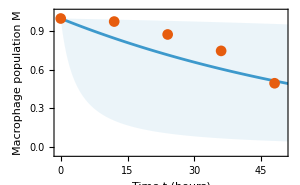
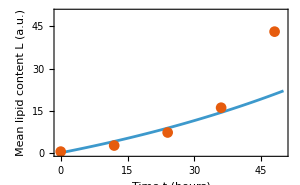
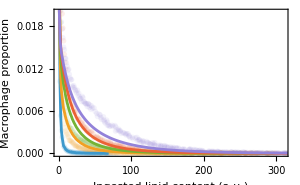
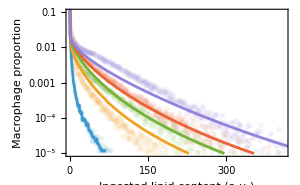
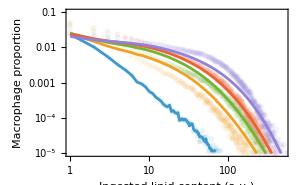
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
plots[{η,100*e,cv,β0/100,0,1,σM,σm}/.{η->8.329797724416885,e->0.23651925855209982,cv->1.4630311426538278,β0->1.3874366781388838,σM->1.5619064313584106,σm->0.17003144923425417}]
```

```mathematica
(* MLE: βvec = β0*Exp[β1*t] *)
(*η->0.5115191886034228,e->0.4696420279779179,cv->1.0127494644817663,β0->0.1523736773833373,β1->999.9999767738682,q->13.098388912847199*)
nstep=1;
{ηval,eval,cvval,β0val,β1val,σMval,σmval}={0.5115191886034228,0.4696420279779179,1.0127494644817663,0.1523736773833373,1/13.098388912847199,0.15,0.12};
NMaximize[{loglikelihood[{η,100*e,cv,β0/100,β1,1,σM,σm}],0.01<η<1,0.01<e<1,0.01<cv<2,0.01<β0<1,0.01<β1<0.2,0.01<σM<3,0.01<σm<1},{η,e,cv,β0,β1,σM,σm},Method->{Automatic,"InitialPoints"->{{ηval,eval,cvval,β0val,β1val,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{η,e,cv,β0,β1,σM,σm},loglikelihood[{η,100*e,cv,β0/100,β1,1,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.511519,0.469642,1.01275,0.152374,0.0763453,0.15,0.12},48.5941}

Current x: {{0.511252,0.470503,1.00805,0.152959,0.0761321,0.15869,0.120727},48.6153}

{48.6153,{η→0.511252,e→0.470503,cv→1.00805,β0→0.152959,β1→0.0761321,σM→0.15869,σm→0.120727}}

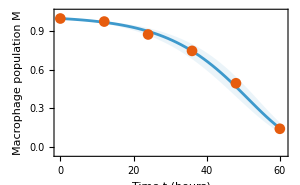
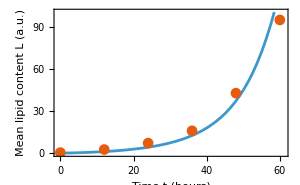
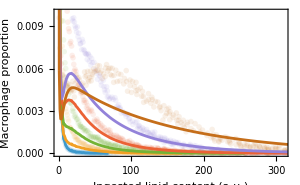
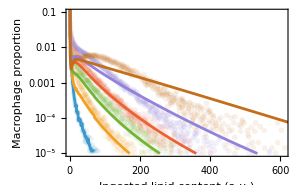
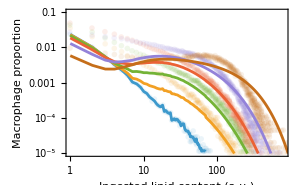
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
plots[{η,100*e,cv,β0/100,β1,1,σM,σm}/.{η->0.5112515343720792,e->0.4705026626154563,cv->1.008046043554522,β0->0.152959233050248,β1->0.0761320852470109,σM->0.15868974905114697,σm->0.12072708514338712}]
```

```mathematica
(* MLE: βvec = β0+β1*idx *)
nstep=1;
{ηval,eval,cvval,β0val,β1val,σMval,σmval}={1,0.2920987303977517,1.2071777574060776,0.4,0.15,0.5,0.5};
NMaximize[{loglikelihood[{η,100*e,cv,β0/100,β1/100,1,σM,σm}],0.1<η<20,0.01<e<1,0.01<cv<2,0.1<β0<10,0.01<β1<1,0.01<σM<3,0.01<σm<1},{η,e,cv,β0,β1,σM,σm},Method->{Automatic,"InitialPoints"->{{ηval,eval,cvval,β0val,β1val,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{η,e,cv,β0,β1,σM,σm},loglikelihood[{η,100*e,cv,β0/100,β1/100,1,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{1.76014,0.260015,0.753005,0.607339,0.13171,0.873673,0.123054},40.3115}

{40.3115,{η→1.76014,e→0.260015,cv→0.753005,β0→0.607339,β1→0.13171,σM→0.873673,σm→0.123054}}

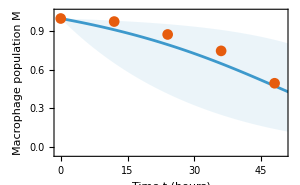
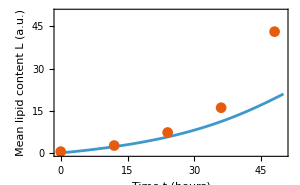
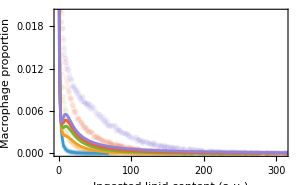
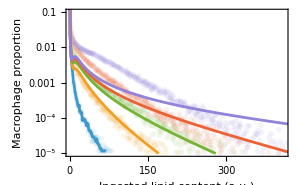
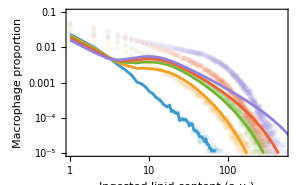
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
plots[{η,100*e,cv,β0/100,β1/100,1,σM,σm}/.{η->1.7601389602565212,e->0.2600147061231354,cv->0.7530051431645146,β0->0.6073391378294042,β1->0.131710185132044,σM->0.8736729259021844,σm->0.12305379800181791}]
```

```mathematica
(* MLE: βvec = β1/(1+(β1-β0)/β0*Exp[-t/q] - tends to β1->Infinity *)
nstep=1;
{ηval,eval,cvval,β0val,β1val,qval,σMval,σmval}={0.12887040181157505,0.45575706198953736,1.3574292200381786,0.13388033142171463,23.846552626229972,11.699642419213806,0.19965437733926822,0.4600729902040419};
NMaximize[{loglikelihood[{η,100*e,cv,β0/100,β1/100,q,σM,σm}],0.01<η<1,0.01<e<1,0.01<cv<2,0.01<β0<1,10<β1<1000,1<q<1000,0.01<σM<3,0.01<σm<1},{η,e,cv,β0,β1,q,σM,σm},Method->{Automatic,"InitialPoints"->{{ηval,eval,cvval,β0val,β1val,qval,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{η,e,cv,β0,β1,q,σM,σm},loglikelihood[{η,100*e,cv,β0/100,β1/100,q,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.12887,0.455757,1.35743,0.13388,23.8466,11.6996,0.199654,0.460073},43.5361}

Current x: {{0.131434,0.458391,1.34888,0.138446,30.7318,12.0375,0.211103,0.458425},43.5668}

{48.6111,{η→0.511519,e→0.469642,cv→1.01275,β0→0.152374,β1→1000.,q→13.0984,σM→0.158694,σm→0.120781}}

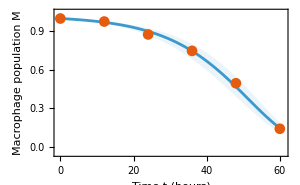
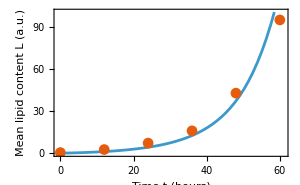
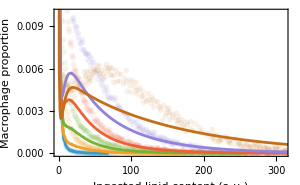
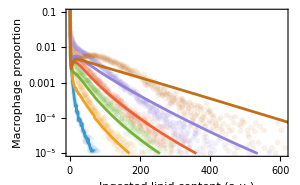
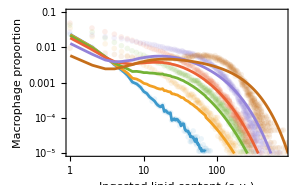
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
plots[{η,100*e,cv,β0/100,β1/100,q,σM,σm}/.{η->0.5115191886034228,e->0.4696420279779179,cv->1.0127494644817663,β0->0.1523736773833373,β1->999.9999767738682,q->13.098388912847199,σM->0.15869373612082566,σm->0.12078081799964269}]
```

```mathematica
(* MLE: βvec = β0+(β1-β0)*(1-Exp[-idx/q] *)
nstep=1;
{ηval,eval,cvval,β0val,β1val,qval,σMval,σmval}={0.43124481131827375,0.4,0.9212300674706696,0.5677803302919306,0.15126469558881683,0.4925970307671418,0.8,0.13};
NMaximize[{loglikelihood[{η,100*e,cv,β0/100,β1,100*q,σM,σm}],0.01<η<10,0.01<e<1,0.01<cv<1,0.01<β0<10,0.01<β1<10,0.01<q<10,0.01<σM<3,0.01<σm<1},{η,e,cv,β0,β1,q,σM,σm},Method->{Automatic,"InitialPoints"->{{ηval,eval,cvval,β0val,β1val,qval,σMval,σmval}}},StepMonitor:>If[Mod[++nstep,50]==0,Print["Current x: ",{{η,e,cv,β0,β1,q,σM,σm},loglikelihood[{η,100*e,cv,β0/100,β1,100*q,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.345584,0.382827,0.917464,0.569431,0.159111,0.739167,0.860421,0.143172},39.2177}

Current x: {{0.804778,0.264037,0.911133,0.692929,0.241895,1.60958,1.01049,0.111645},40.0194}

Current x: {{0.857754,0.252606,0.903509,0.753748,0.242928,1.55115,0.987979,0.108093},40.0865}

Current x: {{1.12732,0.240164,0.905017,0.687962,0.17626,0.86491,0.95108,0.11105},40.1493}

Current x: {{1.25508,0.234087,0.909602,0.701274,0.165198,0.786946,0.952291,0.110313},40.16}

NMaximize::cvmit: Failed to converge to the requested accuracy or precision within 5000 iterations.

{40.1788,{η→1.6772,e→0.221474,cv→0.945546,β0→0.701779,β1→0.150005,q→0.637068,σM→0.954878,σm→0.108892}}

```mathematica
nstep=1;
{ηval,eval,cvval,β0val,β1val,qval,σMval,σmval}={0.43124481131827375,0.3061101407153039,0.9212300674706696,0.5677803302919306,0.15126469558881683,0.4925970307671418,0.8,0.13};
FindMaximum[{loglikelihood[{η,100*e,cv,β0/100,β1,100*q,σM,σm}],0.01<η<10,0.01<e<1,0.01<cv<1,0.01<β0<10,0.01<β1<10,0.01<q<10,0.01<σM<3,0.01<σm<1},{{η,ηval},{e,eval},{cv,cvval},{β0,β0val},{β1,β1val},{q,qval},{σM,σMval},{σm,σmval}},StepMonitor:>If[Mod[++nstep,1]==0,Print["Current x: ",{{η,e,cv,β0,β1,q,σM,σm},loglikelihood[{η,100*e,cv,β0/100,β1,100*q,σM,σm}]}]],WorkingPrecision->MachinePrecision,MaxIterations->5000,PrecisionGoal->5]
```

Current x: {{0.431245,0.30611,0.92123,0.56778,0.151265,0.492597,0.8,0.13},39.583}

Current x: {{0.431245,0.306108,0.921227,0.567781,0.151264,0.492597,0.800002,0.129999},39.583}

Current x: {{0.431249,0.306097,0.921226,0.567786,0.151263,0.492595,0.800007,0.129997},39.5831}

Current x: {{0.431262,0.306065,0.921209,0.56779,0.151267,0.492599,0.800023,0.129991},39.5832}

Current x: {{0.431317,0.306065,0.921154,0.567862,0.151339,0.49261,0.80007,0.129973},39.5835}

$Aborted

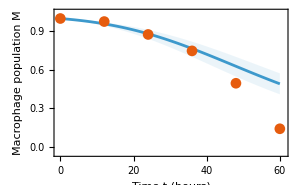
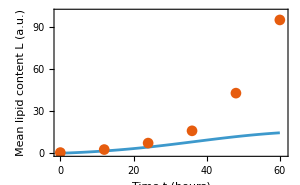
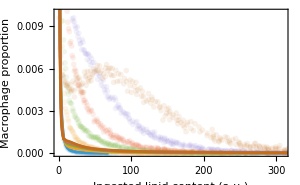
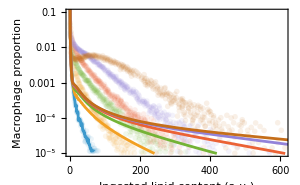
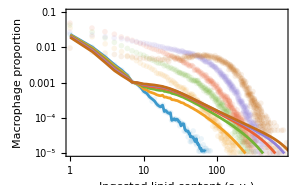
-Graphics- | -Graphics- | 
-Graphics- | -Graphics- | -Graphics-

```mathematica
plots[{η,100*e,cv,β0/100,β1,100*q,σM,σL}/.{η->0.6,e->0.6,cv->1,β0->0.2,β1->1,q->5,σM->0.16782306644744013,σL->0.3179110225867979}]
```